```mathematica
ClearAll[pdf];
pdf[
N1_?NumericQ, 
N2_?NumericQ, 
N3_?NumericQ,
N4_?NumericQ,s
a1_?NumericQ, 
a2_?NumericQ, 
s_]:= pdf[N1, N2, N3, N4, a1, a2, s] = (
in = NIntegrate[
1 * Boole[(N4 - N3 x - N2 y)^2 + (N3 - N2 x - N1 y)^2 < (N4 - N3 a1 - N2 a2)^2 + (N3 - N2 a1 - N1 a2)^2],
 {x, -1, 1}, {y, -1, 1}, WorkingPrecision->8];
s/4(1 - 1/4 Evaluate[Replace[
 in, Except[_?NumericQ] -> 0
]])^(s - 1)
)
```

<a1>: 0.25504026

<a2>: 0.19068579

Std(a1)0.50702787

Std(a2)0.53125612

End of map {71,71,71,71,71,71,71,71,71}

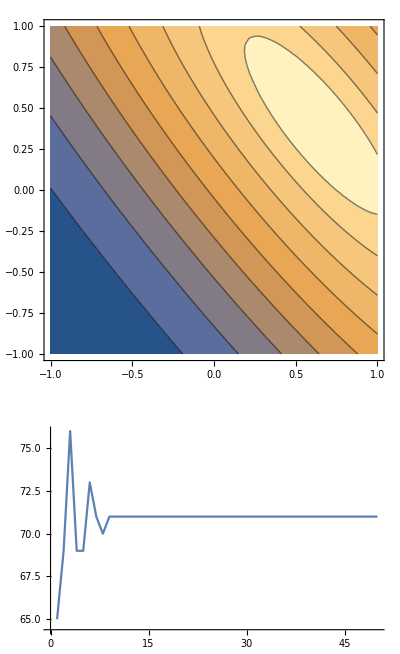

```mathematica
ClearAll[MeanVar]
meanVar[N1_, N2_, N3_, N4_, s_, prec_] := meanVar[N1, N2, N3, N4, s, prec] = (
ea1 = NIntegrate[
a11 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
ea2 = NIntegrate[
a22 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
ea12 = NIntegrate[
a11^2 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
ea22 = NIntegrate[
a22^2 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
{ea1, ea2, Sqrt[ea12 - ea1^2], Sqrt[ea22 - ea2^2]}
)

ClearAll[barMap];
barMap[{N1_, N2_, N3_, N4_, s_, t_, n_, prec_}] := barMap[{N1, N2, N3, N4, s, t, n, prec}] = (
topThreshold = Which[N4 > 0, (t- a22 N3)/N4, N4==0 , 1];
probGo = NIntegrate[
Evaluate[pdf[N1, N2, N3, N4, a11, a22, s]],
{a22, -1, 1},
{a11, -1, Max[-1, Min[1,topThreshold]]},
WorkingPrecision->prec
];

{N2, N3, N4, IntegerPart[n* probGo], s, t, n, prec}
)
ClearAll[barMap];

Clear[fourth]
fourth[ll_] := fourth[ll] = ll[[4]];

ClearAll[runMap];
runMap[N1_, N2_, N3_, N4_, s_, t_, n_, iter_, prec_] := runMap[N1, N2, N3, N4, s, t, n, iter, prec] = (
maps = Reap[Nest[(Sow[barMap[#]])&, {N1,N2, N3, N4,s, t, n, prec},iter]];
fourth/@ maps[[2,1]]
)

ClearAll[describeSim];
describeSim[N1_, N2_, N3_, N4_, s_, t_, n_, iter_, prec_] := describeSim[N1, N2, N3, N4, s, t, n, iter, prec] = (
mv = meanVar[N1, N2, N3, N4, s, prec];
Print[StringForm["<a1>: ``", mv[[1]]]];
Print[StringForm["<a2>: ``", mv[[2]]]];

Print[StringForm["Std(a1)``", mv[[3]]]];
Print[StringForm["Std(a2)``", mv[[4]]]];

p1 = ContourPlot[pdf[N1, N2, N3, N4, a1, a2,s], {a1,-1,1},{a2,-1,1}];

mm = runMap[N1, N2, N3, N4, s, t, n, iter, prec];
p2 = ListPlot[mm, Joined->True];

Print[StringForm["End of map ``", mm[[-9;;]]]];
GraphicsColumn[{p1, p2}]
)

describeSim[33,95, 74, 85,2, 60, 100, 50,8]
```

<a1>: 0.37565899

<a2>: 0.27560443

Std(a1)0.4432471

Std(a2)0.48883666

End of map {69,65,64,69,65,64,69,65,64}

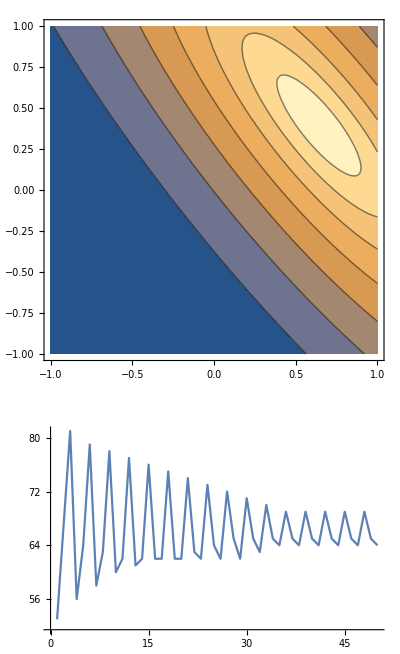

```mathematica
describeSim[33,95, 74, 85,3, 60, 100, 50,8]
```

<a1>: 0.486574

<a2>: 0.35678166

Std(a1)0.3576754

Std(a2)0.4201416

End of map {88,29,88,88,29,88,88,29,88}

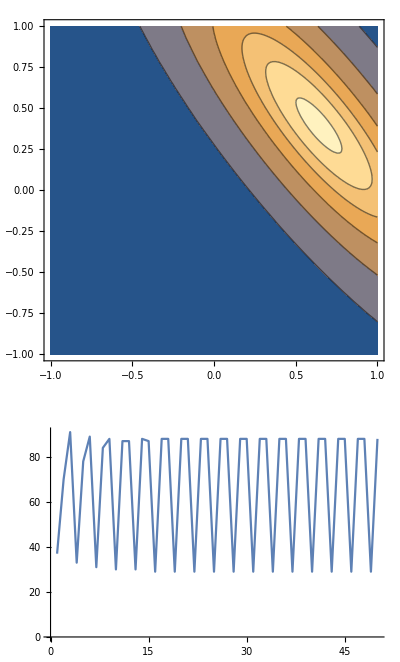

```mathematica
describeSim[33,95, 74, 85,5, 60, 100, 50,8]
```

<a1>: 0.57240592

<a2>: 0.41248081

Std(a1)0.2647929

Std(a2)0.3234714

End of map {99,7,99,99,7,99,99,7,99}

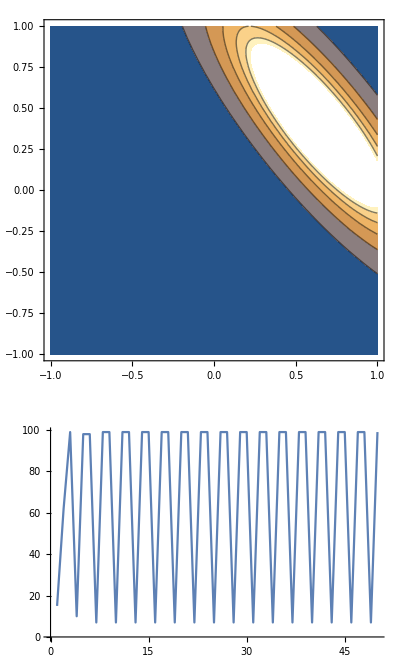

```mathematica
describeSim[33,95, 74, 85,10, 60, 100, 50,8]
```

<a1>: 0.614522

<a2>: 0.414414

Std(a1)0.2071

Std(a2)0.2454

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

End of map {100,0,100,114,0,100,100,0,100}

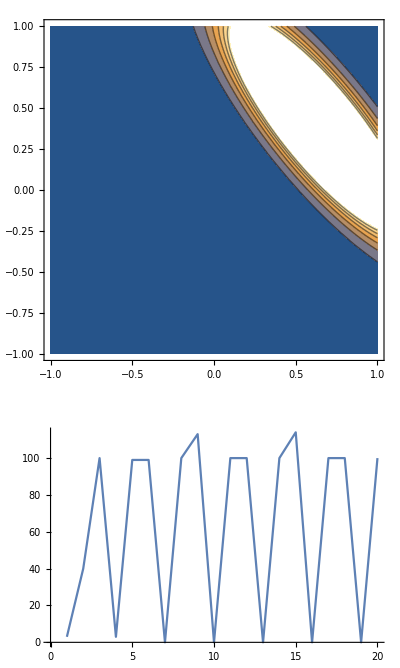

```mathematica
describeSim[33,95, 74, 85,20, 60, 100, 20,6]
```

<a1>: 0.641397

<a2>: 0.394841

Std(a1)0.09972

Std(a2)0.1177

End of map {100,0,100,100,0,100,100,0,100}

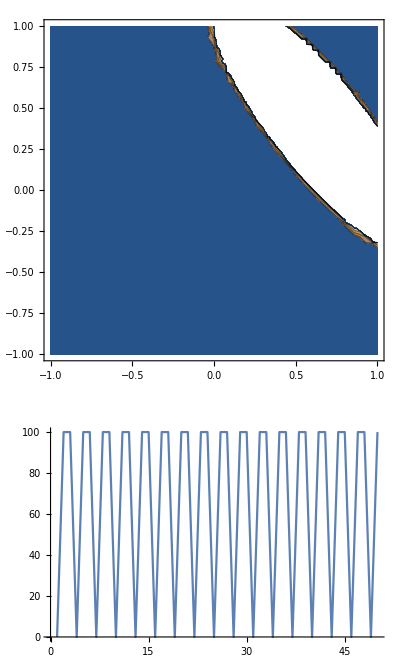

```mathematica
describeSim[33,95, 74, 85,100, 60, 100, 50,6]
```

Try another history!
h=[79, 29,6, 39]

<a1>: -0.0078963309

<a2>: 0.16853965

Std(a1)0.57197182

Std(a2)0.4453335

End of map {71,71,71,71,71,71,71,71,71}

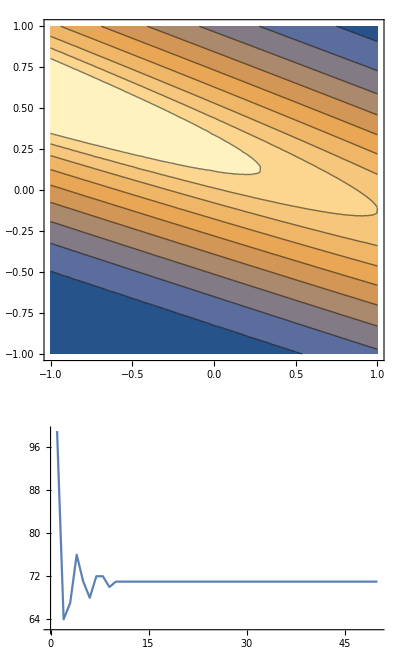

```mathematica
describeSim[79,29,6,39,2, 60, 100, 50, 8]
```

<a1>: -0.057906173

<a2>: 0.22485724

Std(a1)0.5701886

Std(a2)0.3697855

End of map {64,69,65,64,69,65,64,69,65}

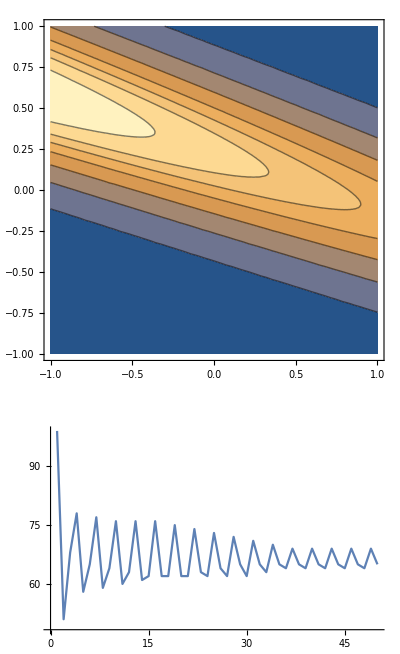

```mathematica
describeSim[79,29,6,39,3, 60, 100, 50,8]
```

<a1>: -0.14927087

<a2>: 0.27425871

Std(a1)0.55853433

Std(a2)0.2948338

End of map {88,88,29,88,88,29,88,88,29}

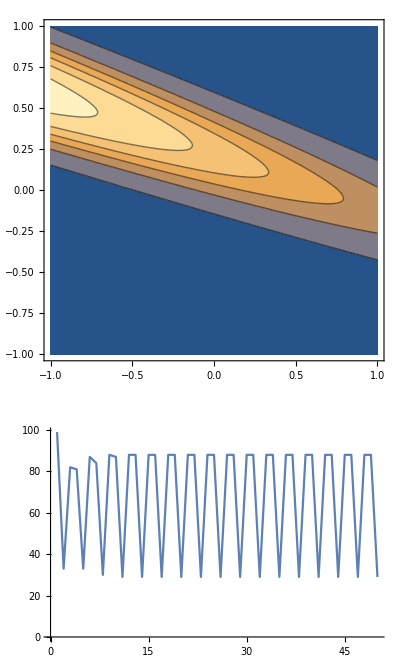

```mathematica
describeSim[79,29,6,39,5, 60, 100, 50,8]
```

<a1>: -0.3234088

<a2>: 0.33897026

Std(a1)0.5034478

Std(a2)0.224781

End of map {99,99,7,99,99,7,99,99,7}

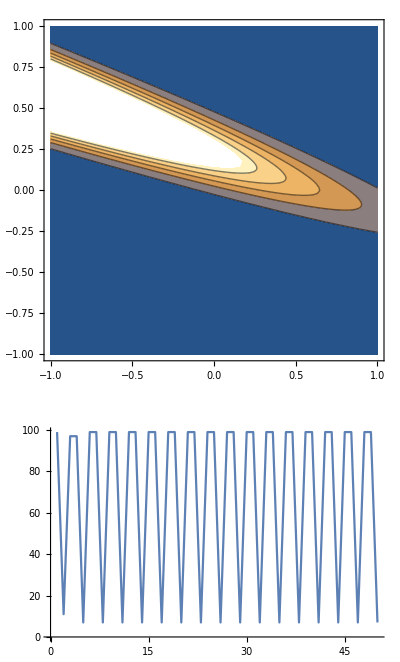

```mathematica
describeSim[79,29,6,39,10, 60, 100, 50,8]
```

<a1>: -0.52593

<a2>: 0.40966

Std(a1)0.3885

Std(a2)0.1691

End of map {100,100,0,100,114,0,106,99,0}

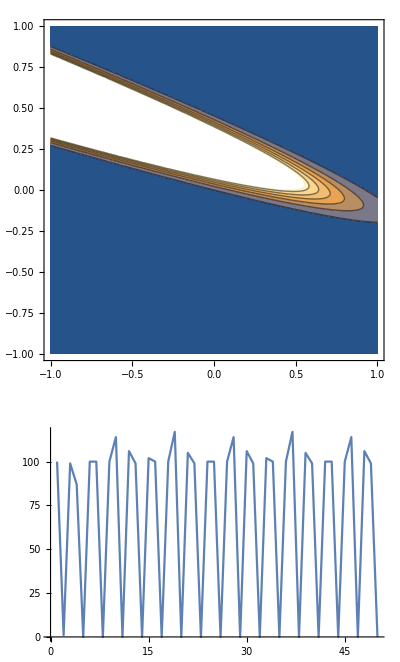

```mathematica
describeSim[79,29,6,39,20, 60, 100, 50,5]
```

<a1>: -0.82743

<a2>: 0.51449

Std(a1)0.147

Std(a2)0.082

End of map {100,100,0,100,100,0,100,100,0}

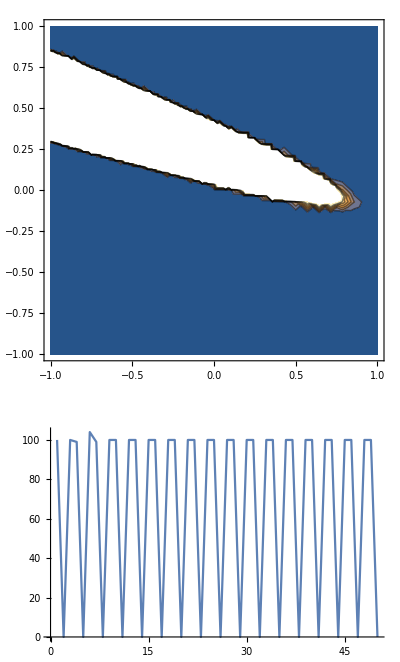

```mathematica
describeSim[79,29,6,39,100, 60, 100, 50,5]
```

<a1>: 0.28122705

<a2>: 0.13800352

Std(a1)0.49904252

Std(a2)0.54323111

End of map {71,71,71,71,71,71,71,71,71}

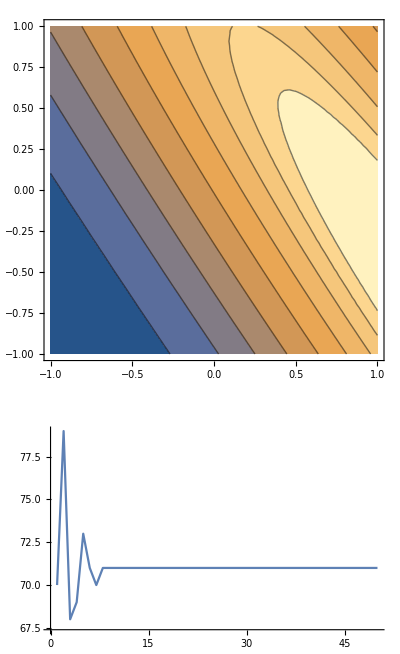

```mathematica
describeSim[33,80,90,60,2, 60, 100, 50,8]
```

<a1>: 0.41754905

<a2>: 0.17606881

Std(a1)0.4292362

Std(a2)0.516569

End of map {65,64,69,65,64,69,65,64,69}

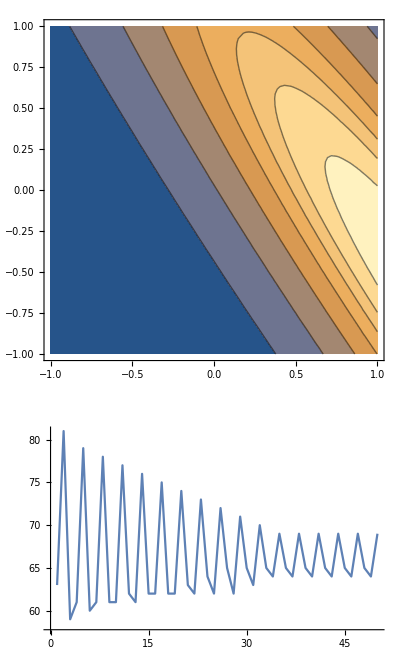

```mathematica
describeSim[33,80,90,60,3, 60, 100, 50,8]
```

<a1>: 0.55095472

<a2>: 0.18378683

Std(a1)0.3385505

Std(a2)0.47365017

End of map {29,88,88,29,88,88,29,88,88}

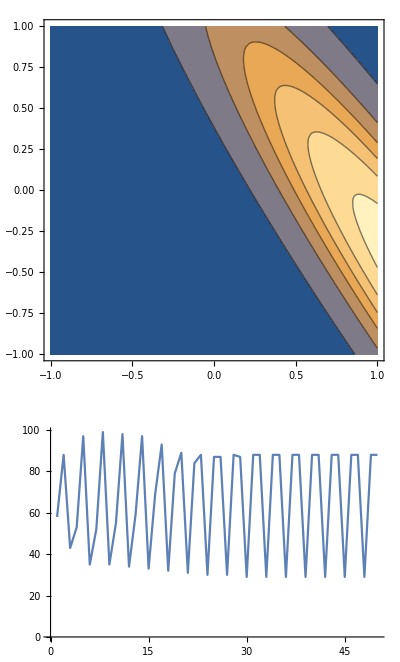

```mathematica
describeSim[33,80,90,60,5, 60, 100, 50,8]
```

<a1>: 0.67531176

<a2>: 0.12698578

Std(a1)0.247335

Std(a2)0.40093298

End of map {7,99,99,7,99,99,7,99,99}

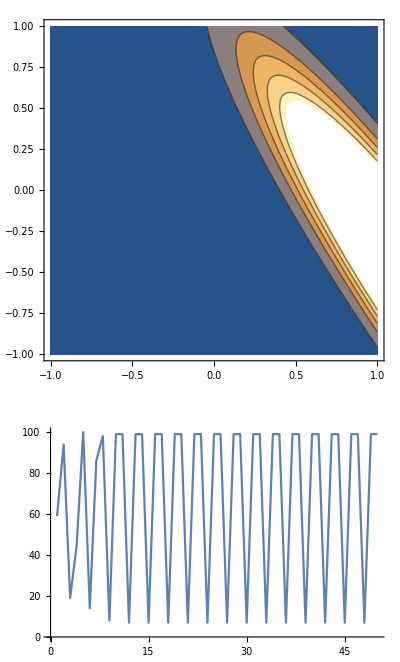

```mathematica
describeSim[33,80,90,60,10, 60, 100, 50,8]
```

<a1>: 0.771719

<a2>: 0.0223813

Std(a1)0.1801

Std(a2)0.313677

End of map {0,100,114,0,100,100,0,100,114}

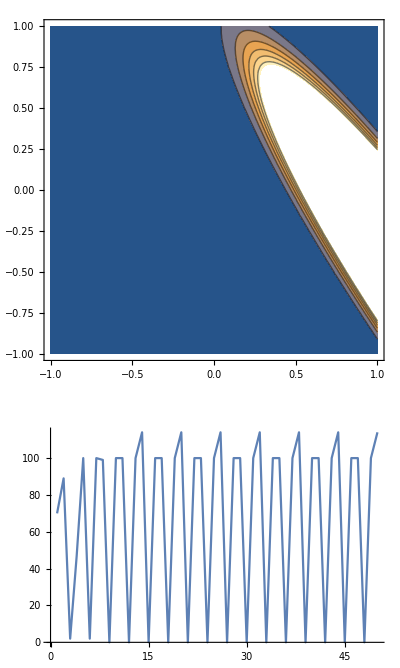

```mathematica
describeSim[33,80,90,60,20, 60, 100, 50,6]
```

<a1>: 0.911628

<a2>: -0.160342

Std(a1)0.0738

Std(a2)0.14773

End of map {0,100,100,0,100,100,0,100,100}

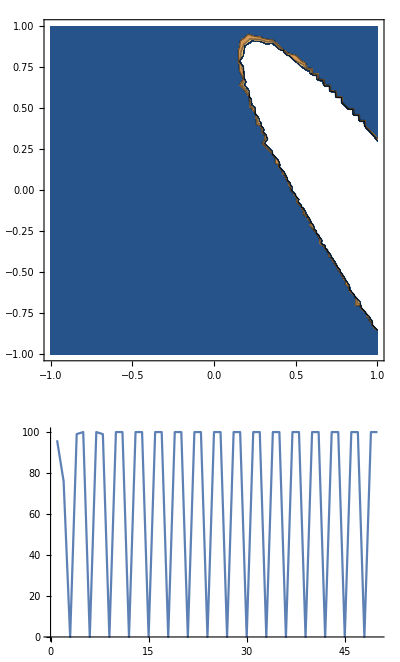

```mathematica
describeSim[33,80,90,60,100, 60, 100, 50,6]
```